https://community.wolfram.com/groups/-/m/t/2293868

#### Import data from Yahoo

```mathematica
ClearAll["Global`*"];
```

```mathematica
AbsoluteTiming[lsData=Import["https://finance.yahoo.com/cryptocurrencies","Data"];]
```

{18.7505,Null}

Interested in the table, locate the table

```mathematica
pos=First@Position[lsData,{"Symbol","Name","Price (Intraday)","Change","% Change",___}];
dsCryptoCurrenciesColumnNames=lsData[[Sequence@@pos]]
Length[dsCryptoCurrenciesColumnNames]
```

{Symbol,Name,Price (Intraday),Change,% Change,Market Cap,Volume in Currency (Since 0:00 UTC),Volume in Currency (24Hr),Total Volume All Currencies (24Hr),Circulating Supply,52 Week Range,1 Day Chart}

12

```mathematica
dsCryptoCurrencies=lsData[[Sequence@@Append[Most[pos],2]]];
Dimensions[dsCryptoCurrencies]
```

{25,10}

```mathematica
dsCryptoCurrencies=Dataset[dsCryptoCurrencies][All,AssociationThread[dsCryptoCurrenciesColumnNames⟦1;;-3⟧,#]&]
```

Symbol | Name | Price (Intraday) | Change | % Change | Market Cap | Volume in Currency (Since 0:00 UTC) | Volume in Currency (24Hr) | Total Volume All Currencies (24Hr) | Circulating Supply
BTC-USD | Bitcoin USD | 33,048.37 | +1,722.36 | +5.50% | 619.445B | 33.843B | 33.843B | 33.843B | 18.744M
ETH-USD | Ethereum USD | 1,836.57 | 58.72 | +3.30% | 213.892B | 18.774B | 18.774B | 18.774B | 116.462M
USDT-USD | Tether USD | 1.0008 | 0.0003 | +0.03% | 62.576B | 50.375B | 50.375B | 50.375B | 62.525B
BNB-USD | BinanceCoin USD | 275.63 | 2.52 | +0.92% | 42.291B | 1.427B | 1.427B | 1.427B | 153.433M
ADA-USD | Cardano USD | 1.2593 | 0.0215 | +1.74% | 40.232B | 2.153B | 2.153B | 2.153B | 31.946B
DOGE-USD | Dogecoin USD | 0.24261 | 0.003611 | +1.51% | 31.588B | 1.783B | 1.783B | 1.783B | 130.201B
XRP-USD | XRP USD | 0.605756 | 0.004665 | +0.78% | 28.013B | 2.169B | 2.169B | 2.169B | 46.245B
USDC-USD | USDCoin USD | 1.0007 | 0.0002 | +0.02% | 25.787B | 1.899B | 1.899B | 1.899B | 25.768B
DOT1-USD | Polkadot USD | 14.32 | 0.25 | +1.77% | 13.677B | 944.825M | 944.825M | 944.825M | 955.371M
HEX-USD | HEX USD | 0.074207 | 0.004849 | +6.99% | 12.868B | 27.512M | 27.512M | 27.512M | 173.411B
UNI3-USD | Uniswap USD | 16.01 | 0.07 | +0.46% | 9.208B | 261.089M | 261.089M | 261.089M | 575.227M
BCH-USD | BitcoinCash USD | 453.67 | 11.05 | +2.50% | 8.517B | 1.273B | 1.273B | 1.273B | 18.775M
LTC-USD | Litecoin USD | 126.95 | 3.74 | +3.04% | 8.474B | 1.706B | 1.706B | 1.706B | 66.752M
SOL1-USD | Solana USD | 30.07 | 1.81 | +6.40% | 8.199B | 465.668M | 465.668M | 465.668M | 272.637M
LINK-USD | Chainlink USD | 16.87 | 0.45 | +2.72% | 7.347B | 752.656M | 752.656M | 752.656M | 435.51M
MATIC-USD | MaticNetwork USD | 1.0438 | 0.0043 | +0.41% | 6.58B | 645.041M | 645.041M | 645.041M | 6.303B
⋮_9 |  |  |  |  |  |  |  |  | 
2 levels | 25rows |  |  |  |  |  |  |  |  | Dataset[{__Association}]

#### Get time series

```mathematica
csvToDataset1[csv_]:=Module[{first=First[csv],rest=Rest[csv]},
Dataset[AssociationThread[first->#]&/@rest]
];
(* version 2 doesn't work *)
csvToDataset2[csv_]:=Dataset[csv][All,AssociationThread[First[csv],#]&];
```

```mathematica
AbsoluteTiming[ccNow=Round@AbsoluteTime[Date[]]-AbsoluteTime[{1970,1,1,0,0,0}];
aCryptoCurrenciesDataRaw=Association@Map[#->csvToDataset1[Import["https://query1.finance.yahoo.com/v7/finance/download/"<>#<>"?period1=1410825600&period2="<>ToString[ccNow]<>"&interval=1d&events=history&includeAdjustedClose=true"]]&,Normal[dsCryptoCurrencies[All,"Symbol"]]];]
```

{11.2922,Null}

```mathematica
aCryptoCurrenciesDataRaw;
Dimensions/@aCryptoCurrenciesDataRaw
```

<|BTC-USD→{2476,7},ETH-USD→{2152,7},USDT-USD→{2315,7},BNB-USD→{1434,7},ADA-USD→{1366,7},DOGE-USD→{2476,7},XRP-USD→{2476,7},USDC-USD→{994,7},DOT1-USD→{312,7},HEX-USD→{559,7},UNI3-USD→{89,7},BCH-USD→{1436,7},LTC-USD→{2476,7},SOL1-USD→{444,7},LINK-USD→{1377,7},MATIC-USD→{792,7},THETA-USD→{1258,7},XLM-USD→{2476,7},ICP1-USD→{40,7},VET-USD→{1060,7},ETC-USD→{1800,7},TRX-USD→{1384,7},FIL-USD→{1293,7},XMR-USD→{2476,7},EOS-USD→{1458,7}|>

pick a random symbol and show 6 rows of data

```mathematica
RandomSample[#,6]&/@KeyTake[aCryptoCurrenciesDataRaw,RandomChoice[Keys@aCryptoCurrenciesDataRaw]]
```

<|HEX-USD→Date | Open | High | Low | Close | Adj Close | Volume
2020-11-02 | null | null | null | null | null | null
2020-11-19 | null | null | null | null | null | null
2020-07-03 | 0.003299 | 0.003311 | 0.003152 | 0.003205 | 0.003205 | 1004284
2020-09-16 | null | null | null | null | null | null
2020-10-13 | null | null | null | null | null | null
2020-08-17 | 0.002943 | 0.00303 | 0.00275 | 0.00275 | 0.00275 | 1313692
2 levels | 6rows |  |  |  |  |  | Dataset[{__Association}]|>

```mathematica
AbsoluteTiming[aCryptoCurrenciesData=Association@KeyValueMap[Function[{k,v},k->v[All,Join[<|"Symbol"->k,"DateObject"->DateObject[#Date]|>,#]&]],aCryptoCurrenciesDataRaw];]
```

{15.5157,Null}

```mathematica
RandomSample[#,6]&/@KeyTake[aCryptoCurrenciesData,RandomChoice[Keys@aCryptoCurrenciesData]]
```

<|BTC-USD→Symbol | DateObject | Date | Open | High | Low | Close | Adj Close | Volume
BTC-USD | 25 Jul 2015 | 2015-07-25 | 288.2 | 290.7 | 286. | 288.7 | 288.7 | 20662200
BTC-USD | 10 Feb 2017 | 2017-02-10 | 995.6 | 998.9 | 946.7 | 988.7 | 988.7 | 190452000
BTC-USD | 26 Dec 2015 | 2015-12-26 | 455.8 | 457.5 | 405.8 | 417.3 | 417.3 | 116166000
BTC-USD | 8 Oct 2018 | 2018-10-08 | 6600. | 6675. | 6576. | 6652. | 6652. | 3979460000
BTC-USD | 24 Nov 2019 | 2019-11-24 | 7399. | 7409. | 7029. | 7048. | 7048. | 30433517289
BTC-USD | 6 Dec 2020 | 2020-12-06 | 19150. | 19390. | 18900. | 19350. | 19350. | 25293775714
2 levels | 6rows |  |  |  |  |  |  |  | Dataset[{__Association}]|>

#### Plot time series

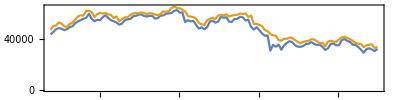
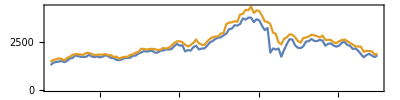
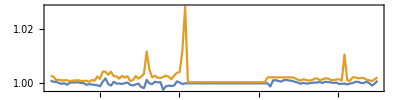
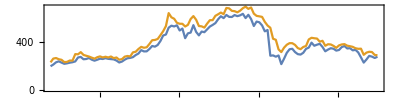
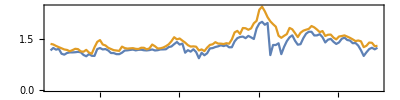
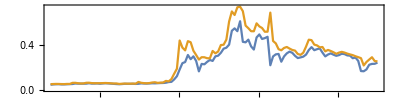
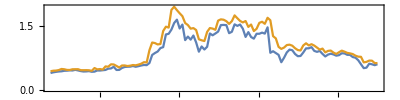
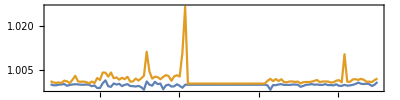
<|BTC-USD→-Graphics-,ETH-USD→-Graphics-,USDT-USD→-Graphics-,BNB-USD→-Graphics-,ADA-USD→-Graphics-,DOGE-USD→-Graphics-,XRP-USD→-Graphics-,USDC-USD→-Graphics-,DOT1-USD→-Graphics-,HEX-USD→-Graphics-,UNI3-USD→-Graphics-,BCH-USD→-Graphics-,LTC-USD→-Graphics-,SOL1-USD→-Graphics-,LINK-USD→-Graphics-,MATIC-USD→-Graphics-,THETA-USD→-Graphics-,XLM-USD→-Graphics-,ICP1-USD→-Graphics-,VET-USD→-Graphics-,ETC-USD→-Graphics-,TRX-USD→-Graphics-,FIL-USD→-Graphics-,XMR-USD→-Graphics-,EOS-USD→-Graphics-|>

```mathematica
nDays=120;
Map[Block[{dsTemp=#[Select[AbsoluteTime[#DateObject]>AbsoluteTime[DatePlus[Now,-Quantity[nDays,"Days"]]]&]]},DateListPlot[{Normal[dsTemp[All,{"DateObject","Low"}][Values]],Normal[dsTemp[All,{"DateObject","High"}][Values]]},PlotLegends->{"Low","High"},AspectRatio->1/4,PlotRange->All]]&,aCryptoCurrenciesData]
```

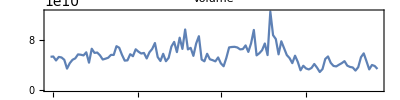
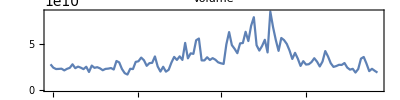
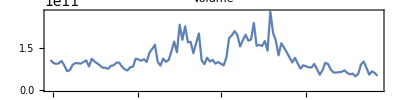
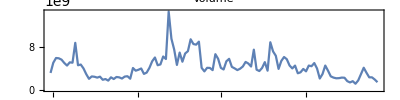
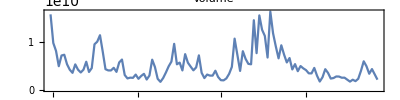
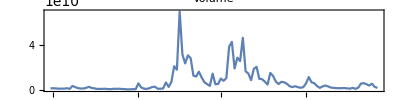
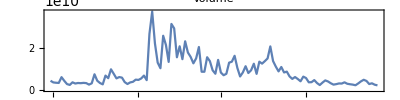
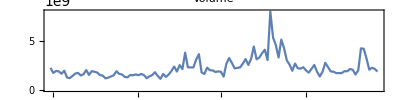
<|BTC-USD→-Graphics-,ETH-USD→-Graphics-,USDT-USD→-Graphics-,BNB-USD→-Graphics-,ADA-USD→-Graphics-,DOGE-USD→-Graphics-,XRP-USD→-Graphics-,USDC-USD→-Graphics-,DOT1-USD→-Graphics-,HEX-USD→-Graphics-,UNI3-USD→-Graphics-,BCH-USD→-Graphics-,LTC-USD→-Graphics-,SOL1-USD→-Graphics-,LINK-USD→-Graphics-,MATIC-USD→-Graphics-,THETA-USD→-Graphics-,XLM-USD→-Graphics-,ICP1-USD→-Graphics-,VET-USD→-Graphics-,ETC-USD→-Graphics-,TRX-USD→-Graphics-,FIL-USD→-Graphics-,XMR-USD→-Graphics-,EOS-USD→-Graphics-|>

```mathematica
nDays=120;
Map[Block[{dsTemp=#[Select[AbsoluteTime[#DateObject]>AbsoluteTime[DatePlus[Now,-Quantity[nDays,"Days"]]]&]]},DateListPlot[{Normal[dsTemp[All,{"DateObject","Volume"}][Values]]},PlotLabel->"Volume",AspectRatio->1/4,PlotRange->All]]&,aCryptoCurrenciesData]
```

#### data.bitcoinity.org

import data for defining met-data.

```mathematica
Import["https://data.bitcoinity.org/markets/price/30d/USD?t=l","Plaintext"]
```

```mathematica
lsCurrencies={"all","AED","ARS","AUD","BRL","CAD","CHF","CLP","CNY","COP","CZK","DKK","EUR","GBP","HKD","HRK","HUF","IDR","ILS","INR","IRR","JPY","KES","KRW","MXN","MYR","NOK","NZD","PHP","PKR","PLN","RON","RUB","RUR","SAR","SEK","SGD","THB","TRY","UAH","USD","VEF","XAU","ZAR"};
lsExchanges={"all","bit-x","bit2c","bitbay","bitcoin.co.id","bitcoincentral","bitcoinde","bitcoinsnorway","bitcurex","bitfinex","bitflyer","bithumb","bitmarketpl","bitmex","bitquick","bitso","bitstamp","btcchina","btce","btcmarkets","campbx","cex.io","clevercoin","coinbase","coinfloor","exmo","gemini","hitbtc","huobi","itbit","korbit","kraken","lakebtc","localbitcoins","mercadobitcoin","okcoin","paymium","quadrigacx","therocktrading","vaultoro","wallofcoins"};
lsTimeSpans={"10m","1h","6h","24h","3d","30d","6m","2y","5y","all"};
lsTimeUnit={"second","minute","hour","day","week","month"};
aDataTypeDescriptions=Association@{"price"->"Prince","volume"->"Trading Volume","rank"->"Rank","bidask_sum"->"Bid/Ask Sum","spread"->"Bid/Ask Spread","tradespm"->"Trades Per Minute"};
lsDataTypes=Keys[aDataTypeDescriptions];
```

```mathematica
stDBOURL=StringTemplate["https://data.bitcoinity.org/export_data.csv?currency=`currency`&data_type=`dataType`&exchange=`exchange`&r=`timeUnit`&t=l&timespan=`timeSpan`"];
aDBODefaultParameters=<|"currency"->"USD","dataType"->"price","exchange"->"all","timeUnit"->"day","timeSpan"->"all"|>;
```

```mathematica
aDBODefaultParameters
Join[aDBODefaultParameters,<|"currency"->"EUR","timeUnit"->"hour","timeSpan"->"30d","exchange"->"coinbase"|>]
```

<|currency→USD,dataType→price,exchange→all,timeUnit→day,timeSpan→all|>

<|currency→EUR,dataType→price,exchange→coinbase,timeUnit→hour,timeSpan→30d|>

```mathematica
dsBTCPriceData=csvToDataset1@Import[stDBOURL[Join[aDBODefaultParameters,<|"currency"->"EUR","timeUnit"->"hour","timeSpan"->"30d","exchange"->"coinbase"|>]]];
```

```mathematica
dsBTCPriceData
```

Time | avg | max | min
2021-05-28 19:00:00 UTC | 29510. | 29990. | 29210.
2021-05-28 20:00:00 UTC | 29280. | 29760. | 28870.
2021-05-28 21:00:00 UTC | 28700. | 29060. | 28450.
2021-05-28 22:00:00 UTC | 28820. | 29220. | 28540.
2021-05-28 23:00:00 UTC | 29130. | 29490. | 28710.
2021-05-29 00:00:00 UTC | 29530. | 29910. | 29270.
2021-05-29 01:00:00 UTC | 29820. | 29970. | 29660.
2021-05-29 02:00:00 UTC | 29840. | 30050. | 29670.
2021-05-29 03:00:00 UTC | 29910. | 30180. | 29700.
2021-05-29 04:00:00 UTC | 29700. | 30090. | 29270.
2021-05-29 05:00:00 UTC | 30200. | 30620. | 29360.
2021-05-29 06:00:00 UTC | 30230. | 30450. | 29970.
2021-05-29 07:00:00 UTC | 29900. | 30150. | 29580.
2021-05-29 08:00:00 UTC | 29570. | 29860. | 29310.
2021-05-29 09:00:00 UTC | 29020. | 29510. | 28680.
2021-05-29 10:00:00 UTC | 29000. | 29190. | 28800.
⋮_703 |  |  | 
2 levels | 719rows |  |  | Dataset[{__Association}]

Volumn data

```mathematica
dsBTCVolumeData=csvToDataset1@Import[stDBOURL[Join[aDBODefaultParameters,<|"dataType"->Volume,"timeUnit"->"day","timeSpan"->"30d","exchange"->"all"|>]]];
```

```mathematica
dsBTCVolumeData
```

Time | bit-x | bitfinex | bitstamp | cex.io | coinbase | exmo | gemini | kraken | others | wallofcoins
2021-05-28 00:00:00 UTC |  | 9994. | 6019. | 426.6 | 35120. | 185.8 | 3383. | 8826. |  | 0.0253634
2021-05-29 00:00:00 UTC |  | 7763. | 4457. | 460.5 | 28000. | 227.8 | 2160. | 5845. |  | 
2021-05-30 00:00:00 UTC |  | 6017. | 2980. | 199.8 | 16040. | 133.4 | 1512. | 4455. |  | 
2021-05-31 00:00:00 UTC |  | 5975. | 4384. | 208. | 19530. | 164.7 | 1855. | 6225. |  | 
2021-06-01 00:00:00 UTC |  | 5285. | 4349. | 221.2 | 15710. | 159. | 2269. | 5703. |  | 
2021-06-02 00:00:00 UTC |  | 3971. | 4270. | 131.9 | 13950. | 160.4 | 1752. | 6308. |  | 
2021-06-03 00:00:00 UTC |  | 5755. | 4059. | 138.9 | 14330. | 156.7 | 1593. | 5230. |  | 
2021-06-04 00:00:00 UTC |  | 5931. | 5786. | 269.4 | 17920. | 179.4 | 2380. | 4992. |  | 
2021-06-05 00:00:00 UTC |  | 6588. | 4106. | 199.9 | 13650. | 163.6 | 2474. | 5533. |  | 
2021-06-06 00:00:00 UTC |  | 6511. | 2527. | 107.5 | 8185. | 146.9 | 998.2 | 3188. |  | 
2021-06-07 00:00:00 UTC | 0.0001 | 9968. | 4913. | 155.2 | 19000. | 149.8 | 2518. | 6166. |  | 
2021-06-08 00:00:00 UTC |  | 12920. | 9045. | 296.8 | 34940. | 217.2 | 6055. | 10550. |  | 
2021-06-09 00:00:00 UTC |  | 26970. | 8540. | 333.4 | 26040. | 218.4 | 4231. | 9357. |  | 
2021-06-10 00:00:00 UTC |  | 9567. | 5762. | 298. | 19850. | 170.3 | 2952. | 7733. |  | 
2021-06-11 00:00:00 UTC |  | 6417. | 3741. | 203.7 | 14140. | 150.3 | 1859. | 5218. |  | 
2021-06-12 00:00:00 UTC |  | 7376. | 3728. | 222.1 | 14520. | 141.2 | 1605. | 5765. |  | 
⋮_14 |  |  |  |  |  |  |  |  |  | 
2 levels | 30rows |  |  |  |  |  |  |  |  |  | Dataset[{__Association}]

#### Plot

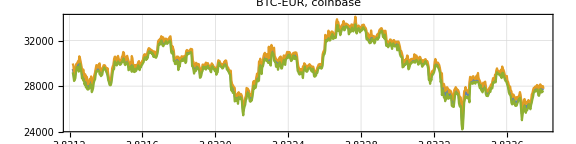

```mathematica
DateListPlot[Association[#->Normal[dsBTCPriceData[All,{"Time",#}][Values]]&/@Rest[Normal[Keys[dsBTCPriceData⟦1⟧]]]],AspectRatio->1/4,ImageSize->Large,PlotLabel->Row[{"BTC-EUR, coinbase"}],PlotTheme->"Detailed"]
```

```mathematica
Rest@Normal@Keys@dsBTCPriceData[[1]]
```

{avg,max,min}

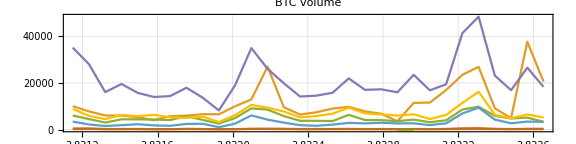

```mathematica
DateListPlot[Association[#->Normal[dsBTCVolumeData[All,{"Time",#}][Values]]&/@Rest[Normal[Keys[dsBTCVolumeData⟦1⟧]]]],PlotRange->All,AspectRatio->1/4,ImageSize->Large,PlotLabel->Row[{"BTC volume"}],PlotTheme->"Detailed",GridLines->Automatic]
```